```mathematica
CompanionMatrix[p_, x_] := Module[{cl=CoefficientList[p, x], deg, m}, cl=Drop[cl/Last[cl], -1]; deg=Length[cl]; If[deg==1, {-cl}, m=RotateLeft[IdentityMatrix[deg]]; m[[ -1]]=-cl; Transpose[m]]];
```

```mathematica
p[x_,n_]=x^(2*n)-I*n*Sqrt[3]*x^n+1
```

1-ⅈ √3 n x^n+x^(2 n)

```mathematica
Table[p[x,i],{i,1,10}]
```

{1-ⅈ √3 x+x^2,1-2 ⅈ √3 x^2+x^4,1-3 ⅈ √3 x^3+x^6,1-4 ⅈ √3 x^4+x^8,1-5 ⅈ √3 x^5+x^10,1-6 ⅈ √3 x^6+x^12,1-7 ⅈ √3 x^7+x^14,1-8 ⅈ √3 x^8+x^16,1-9 ⅈ √3 x^9+x^18,1-10 ⅈ √3 x^10+x^20}

```mathematica
Table[x/.NSolve[p[x,i]==0,x],{i,1,10}]
```

{{0.-0.45685 ⅈ,0.+2.1889 ⅈ},{-1.36603-1.36603 ⅈ,-0.366025+0.366025 ⅈ,0.366025-0.366025 ⅈ,1.36603+1.36603 ⅈ},{-1.51767+0.876227 ⅈ,-0.494179-0.285314 ⅈ,0.+0.570628 ⅈ,0.-1.75245 ⅈ,0.494179-0.285314 ⅈ,1.51767+0.876227 ⅈ},{-1.50649-0.624007 ⅈ,-0.624007+1.50649 ⅈ,-0.566586+0.234688 ⅈ,-0.234688-0.566586 ⅈ,0.234688+0.566586 ⅈ,0.566586-0.234688 ⅈ,0.624007-1.50649 ⅈ,1.50649+0.624007 ⅈ},{-1.46841+0.477116 ⅈ,-0.907529-1.24911 ⅈ,-0.615977-0.200143 ⅈ,-0.380695+0.523981 ⅈ,0.-0.647677 ⅈ,0.+1.54398 ⅈ,0.380695+0.523981 ⅈ,0.615977-0.200143 ⅈ,0.907529-1.24911 ⅈ,1.46841+0.477116 ⅈ},{-1.42908-0.382921 ⅈ,-1.04616+1.04616 ⅈ,-0.652876+0.174938 ⅈ,-0.477938-0.477938 ⅈ,-0.382921-1.42908 ⅈ,-0.174938+0.652876 ⅈ,0.174938-0.652876 ⅈ,0.382921+1.42908 ⅈ,0.477938+0.477938 ⅈ,0.652876-0.174938 ⅈ,1.04616-1.04616 ⅈ,1.42908+0.382921 ⅈ},{-1.39379+0.318124 ⅈ,-1.11774-0.891365 ⅈ,-0.68194-0.155648 ⅈ,-0.620297+1.28806 ⅈ,-0.546874+0.436117 ⅈ,-0.303492-0.630208 ⅈ,0.+0.699478 ⅈ,0.-1.42964 ⅈ,0.303492-0.630208 ⅈ,0.546874+0.436117 ⅈ,0.620297+1.28806 ⅈ,0.68194-0.155648 ⅈ,1.11774-0.891365 ⅈ,1.39379+0.318124 ⅈ},{-1.3632-0.271158 ⅈ,-1.15567+0.772193 ⅈ,-0.772193-1.15567 ⅈ,-0.705646+0.140362 ⅈ,-0.598218-0.399717 ⅈ,-0.399717+0.598218 ⅈ,-0.271158+1.3632 ⅈ,-0.140362-0.705646 ⅈ,0.140362+0.705646 ⅈ,0.271158-1.3632 ⅈ,0.399717-0.598218 ⅈ,0.598218+0.399717 ⅈ,0.705646-0.140362 ⅈ,0.772193+1.15567 ⅈ,1.15567-0.772193 ⅈ,1.3632+0.271158 ⅈ},{-1.33685+0.235723 ⅈ,-1.17561-0.678736 ⅈ,-0.872567+1.03988 ⅈ,-0.725472-0.12792 ⅈ,-0.637969+0.368332 ⅈ,-0.473518-0.564317 ⅈ,-0.464283-1.27561 ⅈ,-0.251954+0.692237 ⅈ,0.-0.736663 ⅈ,0.+1.35747 ⅈ,0.251954+0.692237 ⅈ,0.464283-1.27561 ⅈ,0.473518-0.564317 ⅈ,0.637969+0.368332 ⅈ,0.725472-0.12792 ⅈ,0.872567+1.03988 ⅈ,1.17561-0.678736 ⅈ,1.33685+0.235723 ⅈ},{-1.31407-0.208129 ⅈ,-1.18544+0.604014 ⅈ,-0.940774-0.940774 ⅈ,-0.742369+0.11758 ⅈ,-0.669701-0.34123 ⅈ,-0.604014+1.18544 ⅈ,-0.531478+0.531478 ⅈ,-0.34123-0.669701 ⅈ,-0.208129-1.31407 ⅈ,-0.11758+0.742369 ⅈ,0.11758-0.742369 ⅈ,0.208129+1.31407 ⅈ,0.34123+0.669701 ⅈ,0.531478-0.531478 ⅈ,0.604014-1.18544 ⅈ,0.669701+0.34123 ⅈ,0.742369-0.11758 ⅈ,0.940774+0.940774 ⅈ,1.18544-0.604014 ⅈ,1.31407+0.208129 ⅈ}}

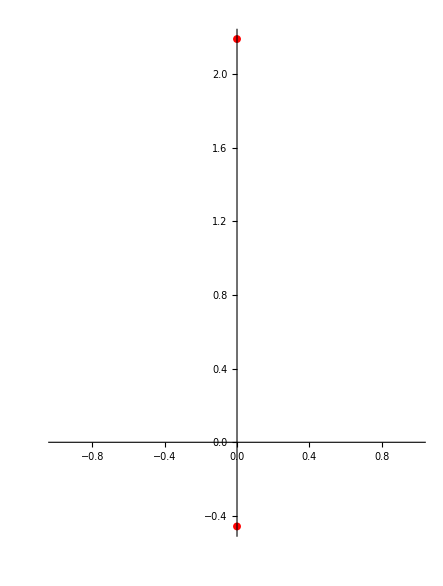
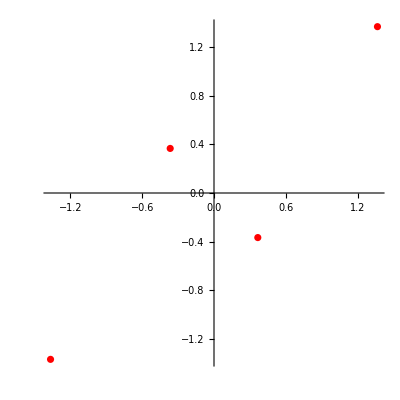
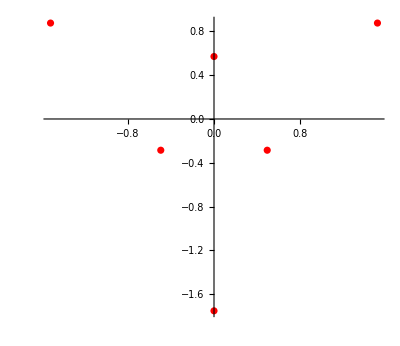
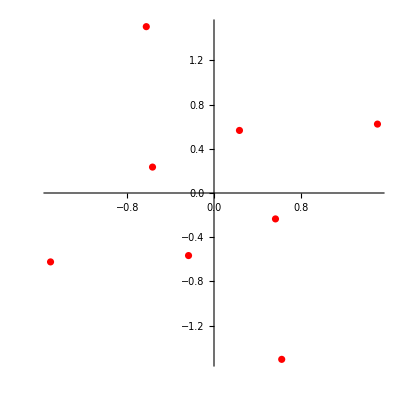
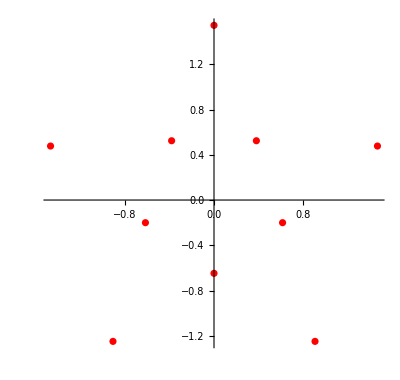
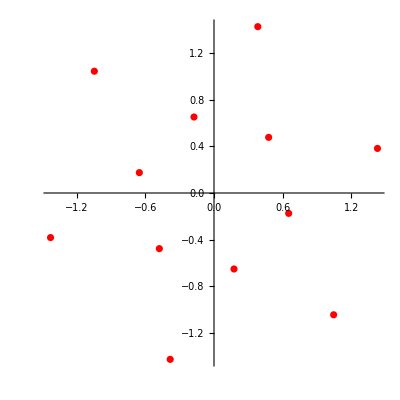
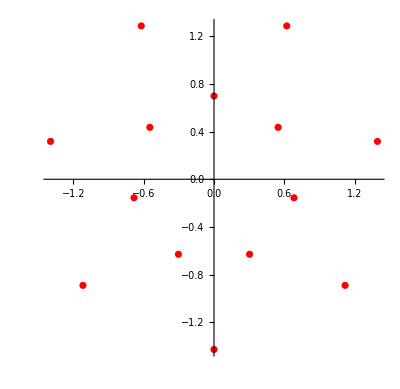
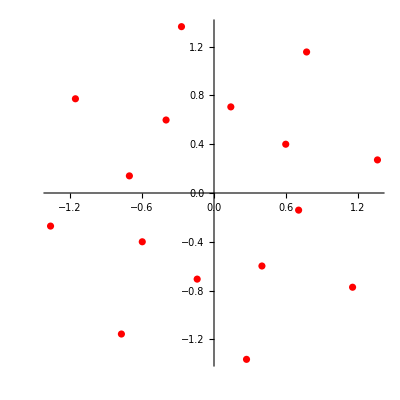

```mathematica
Table[ComplexListPlot[x/.NSolve[p[x,i]==0,x],PlotRange->All,PlotStyle->Red],{i,1,10}]
```

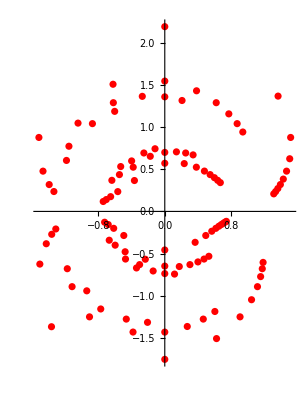

```mathematica
Show[%,PlotRange->All,ImageSize->Full]
```